## Jecco Output Reader

### Extracting boundary velocities

```mathematica
FileName="NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_rec8_all/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_rec8_all";
FolderName="home/giulio/University/PhD/Simulations/";
TypeOfFile={"bulk","gauge","constrained"};
init=4262601;
end=4262602;
each=1;
FNames=Table[Table[StringJoin[TypeOfFile[[ii]]<>"_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}],{ii,1,3}];
Name2=Table[Table[StringJoin["/"<>FolderName<>FileName<>"/",
FNames[[ii,i]],".h5"],{i,FNames[[1]]//Length}],{ii,1,3}];
dt=Import[Name2[[-1,-1]],"Attributes"][[3,1]];
Timing[Obj=Module[{lastValid},Table[If[FileExistsQ[Name2[[ii,i]]],lastValid=Import[Name2[[ii,i]],"Data"];
lastValid,lastValid (*reuse previous if missing*)],{i,1,Length[Name2[[2]]]},{ii,1,3}]];
(*Obj=Table[Import[Name1[[i]],"Data"](*[[1]]*),{i,1,Name1//Length}]*)];//AbsoluteTiming
Print["you have imported: "<>ToString[FNames[[1]]//Length]<>" snapshot"];
(*"/home/giulio/University/PhD/JeccoGt2/examples/BB_QNM_1D_4p1_Vchannel_xpert/"*)
Print["defining times vector ..."]
times=Table[tim dt each+init dt,{tim,1,Obj//Length}];
(*snapshots=Table[(tim-1)  each+init ,{tim,1,Obj//Length}];*)
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[Name2[[-1,-1]],"Attributes"][[3,2]]//FullForm]]
```

{0.147977,Null}

you have imported: 2 snapshot

defining times vector ...

dt = 0.219

final time = 933509.8379952463`

#### Grid

It’s usefull to have the XY grid explicitly in order to make more understandable plots.
Usually, I just import it from the initialdata notebook, but the X and Y grids are cartesian and equally spaced, so if you know the domain used it will be straightforward to create the grid calling a function like Range or Table (this information and also the number of points are contained in the parameter file that is usually in the output folder, together with the actual output data).
Note! In the grid, the last point is not considered!!!
This because of the periodic boundary conditions.

```mathematica
Name1=Name2[[3]];
```

```mathematica
ay=Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
by=-Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
Ly=ay-by;
ax=Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
bx=-Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
Lx=ax-bx;
NPoints=Obj[[1,1,;;]]//Length
```

4

```mathematica
Import[Name1[[1]],"Attributes"][[5,3]]
```

{-5000.,-30000.,3.3}

```mathematica
Obj[[1,1,1]]//Dimensions
```

{75,450,10}

```mathematica
xValues=Range[bx,ax,(ax 2)/(Obj[[1,1,1,1,;;]]//Length)][[1;;-2]];
yValues=Range[by,ay,(ay 2)/(Obj[[1,1,1,;;]]//Length)][[1;;-2]];
nx=xValues//Length;
ny=yValues//Length;
dx=xValues[[2]]-xValues[[1]];
dy=yValues[[2]]-yValues[[1]];
```

```mathematica
nx
ny
```

450

75

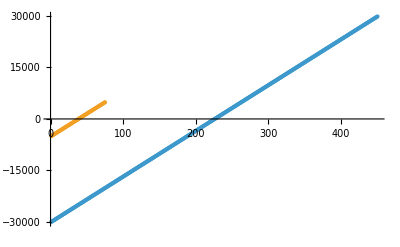

-30000.

29866.7

133.333

```mathematica
ListPlot[{xValues,yValues}]
xValues[[1]]
xValues[[-1]]
dx
```

```mathematica
prec=20
uOuterMin=1/10;(*The boundary of the inner subdomain*)
uOuterMax= 11/10;(*The boundary of the last outer subdomain, should be close to the horizon*)
uOuterDomains=2;(*Number of outer subdomain*)
uOuterNodes=24;(*Number of points in each outer subdomains*)
uInnerNodes=12;(*Number of points in the inner subdomains*)
InterfaceNodes=Table[uOuterMin+i(uOuterMax-uOuterMin)/uOuterDomains,{i,0,uOuterDomains,1}];(*This gives the nodes where the subdomains meet*)
```

20

```mathematica
GetuDomain2[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,1,uOutNodes}],{j,2,IntfaceNodes//Length}],prec];
(*Print[Flatten[uOut,{1}]//Dimensions];*)
Insert[Flatten[uOut,{1}],uInner,1]
]
```

```mathematica
uValues=GetuDomain2[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes];
```

```mathematica
{uValues1,uValues2,uValues3}=uValues;
Nx=nx;
```

```mathematica
Clear[d];
(*d[1,0]=NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xValues,yValues},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,1]=NDSolve`FiniteDifferenceDerivative[Derivative[0,1],{xValues,yValues},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];*)
d[1,0]=NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{Join[xValues,{xValues[[-1]]+dx}],Join[yValues,{yValues[[-1]]+dy}]},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,1]=NDSolve`FiniteDifferenceDerivative[Derivative[0,1],{Join[xValues,{xValues[[-1]]+dx}],Join[yValues,{yValues[[-1]]+dy}]},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
dert=NDSolve`FiniteDifferenceDerivative[Derivative[1,0,0],{times,Join[xValues,{xValues[[-1]]+dx}],Join[yValues,{yValues[[-1]]+dy}]},DifferenceOrder->{4,"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{False,True,True}];
(*d[2,0]=NDSolve`FiniteDifferenceDerivative[Derivative[2,0],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,1]=NDSolve`FiniteDifferenceDerivative[Derivative[0,1],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,2]=NDSolve`FiniteDifferenceDerivative[Derivative[0,2],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,6]=NDSolve`FiniteDifferenceDerivative[Derivative[0,6],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[6,0]=NDSolve`FiniteDifferenceDerivative[Derivative[6,0],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];*)
```

NDSolve`FiniteDifferenceDerivative::ordred: There are insufficient points in dimension 1 to achieve the requested approximation order. Order will be reduced to 1.

#### Checkpoint recovery

```mathematica
(* ======================================================*)(*DIRECTORIES*)(* ======================================================*)checkpointDir="/home/giulio/University/PhD/Simulations/"<>"NBB_gaussian_Lx60000_Ly10000_"<>"3d3iu10_6d6u010_Nx450_Ny75_u0d3_"<>"tzero50000_tau20000_A0d8_s0d5_dt0d219";

recoveryBaseDir="/home/giulio/University/PhD/Simulations/"<>"NBB_gaussian_Lx60000_Ly10000_"<>"3d3iu10_6d6u010_Nx450_Ny75_u0d3_"<>"tzero50000_tau20000_A0d8_s0d5_dt0d219_"<>"recovery";

(*Create main recovery directory*)
CreateDirectory[recoveryBaseDir,CreateIntermediateDirectories->True];

(* ======================================================*)
(*GET CHECKPOINT FILES*)
(* ======================================================*)

files=FileNames["checkpoint_it*.h5",checkpointDir];

files=Sort[files];

Print["Found ",Length[files]," checkpoint files"];

(* ======================================================*)
(*CREATE ONE RECOVERY FOLDER PER CHECKPOINT*)
(* ======================================================*)

Do[file=files[[i]];
base=FileBaseName[file];
iter=StringCases[base,"checkpoint_it"~~x:NumberString:>x][[1]];
recoverDir=FileNameJoin[{recoveryBaseDir,"recover_"<>iter}];
(*Create recovery folder*)CreateDirectory[recoverDir,CreateIntermediateDirectories->True];
(*Create symbolic link to checkpoint*)Run["ln -sf "<>file<>" "<>FileNameJoin[{recoverDir,"checkpoint_it"<>iter<>".h5"}]];
Print["Created: ",recoverDir];,{i,Length[files]}]

Print["Done."]
```

Found 175 checkpoint files

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00020948

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00042047

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00063152

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00084321

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00105484

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00126482

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00147660

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00168674

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00189745

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00211017

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00232401

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00253804

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00275283

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00296536

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00317693

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00338834

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00360128

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00381368

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00402547

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00423731

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00444859

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00465923

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00487049

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00507836

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00528619

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00549442

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00570265

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00591115

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00611914

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00632636

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00653413

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00674185

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00694937

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00715802

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00736607

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00757325

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00778147

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00798946

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00819708

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00840480

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00861142

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00881811

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00902584

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00923408

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00944179

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00964932

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_00985576

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01006344

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01027028

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01047873

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01069066

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01090365

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01111603

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01132852

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01154048

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01175232

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01196505

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01217674

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01238884

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01260081

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01281235

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01302443

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01323627

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01344822

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01366115

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01387330

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01408620

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01429693

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01450887

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01486240

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01521078

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01556488

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01592118

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01627503

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01662962

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01698258

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01733608

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01768962

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01804064

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01838956

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01874266

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01909437

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01944700

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_01979878

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02015317

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02050493

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02086057

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02121814

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02157237

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02192721

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02228377

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02263963

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02285081

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02306257

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02327281

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02348280

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02369359

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02390429

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02411352

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02432294

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02453456

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02474640

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02495824

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02516974

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02538105

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02559202

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02580385

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02601332

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02622432

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02643438

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02664284

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02685083

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02705943

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02726956

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02747936

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02769148

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02790380

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02811603

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02832759

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02854017

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02875473

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02896735

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02917996

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02939456

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02960839

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_02982366

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03003778

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03025271

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03046901

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03068542

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03089905

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03111229

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03132597

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03153740

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03175034

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03196672

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03217919

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03239601

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03261579

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03284138

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03306383

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03328558

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03350753

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03373205

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03395701

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03418055

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03440443

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03462863

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03485528

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03507941

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03530635

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03553254

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03575777

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03598298

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03620646

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03643068

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03665778

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03688317

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03710841

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03733190

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03755728

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03792205

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03828439

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03864783

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03901185

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03937349

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_03973824

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_04010596

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_04046986

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_04083477

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_04119659

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_04156384

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_04192578

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_04226678

Created: /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/recover_04262600

Done.